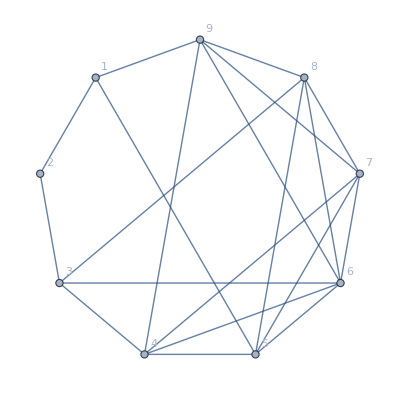

```mathematica
g =Graph[ GraphFromPatterns[First[AllPosibilitiesFor[9,1]]],VertexLabels->"Name"]
```

```mathematica
gr=GroupBy[FindFullFormula[g],SymbolLevel]
```

<|9→{v1x2x3x4x5x6x7x8x9},8→{v1x2x3x4x59x6x7x8,v1x2x3x48x5x6x7x9,v1x2x39x4x5x6x7x8,v1x2x37x4x5x6x8x9,v1x2x35x4x6x7x8x9,v1x29x3x4x5x6x7x8,v1x28x3x4x5x6x7x9,v1x27x3x4x5x6x8x9,v1x26x3x4x5x7x8x9,v1x25x3x4x6x7x8x9,v1x24x3x5x6x7x8x9,v18x2x3x4x5x6x7x9,v17x2x3x4x5x6x8x9,v16x2x3x4x5x7x8x9,v14x2x3x5x6x7x8x9,v13x2x4x5x6x7x8x9},7→{v1x2x3x48x59x6x7,v1x2x39x48x5x6x7,v1x2x37x4x59x6x8,v1x2x37x48x5x6x9,v1x2x359x4x6x7x8,v1x2x35x48x6x7x9,v1x29x3x48x5x6x7,v1x29x37x4x5x6x8,v1x29x35x4x6x7x8,v1x28x3x4x59x6x7,v1x28x39x4x5x6x7,v1x28x37x4x5x6x9,v1x28x35x4x6x7x9,v1x27x3x4x59x6x8,v1x27x3x48x5x6x9,v1x27x39x4x5x6x8,v1x27x35x4x6x8x9,v1x26x3x4x59x7x8,v1x26x3x48x5x7x9,v1x26x39x4x5x7x8,v1x26x37x4x5x8x9,v1x26x35x4x7x8x9,v1x259x3x4x6x7x8,v1x25x3x48x6x7x9,v1x25x39x4x6x7x8,v1x25x37x4x6x8x9,v1x248x3x5x6x7x9,v1x24x3x59x6x7x8,v1x24x39x5x6x7x8,v1x24x37x5x6x8x9,v1x24x35x6x7x8x9,v18x2x3x4x59x6x7,v18x2x39x4x5x6x7,v18x2x37x4x5x6x9,v18x2x35x4x6x7x9,v18x29x3x4x5x6x7,v18x27x3x4x5x6x9,v18x26x3x4x5x7x9,v18x25x3x4x6x7x9,v18x24x3x5x6x7x9,v17x2x3x4x59x6x8,v17x2x3x48x5x6x9,v17x2x39x4x5x6x8,v17x2x35x4x6x8x9,v17x29x3x4x5x6x8,v17x28x3x4x5x6x9,v17x26x3x4x5x8x9,v17x25x3x4x6x8x9,v17x24x3x5x6x8x9,v16x2x3x4x59x7x8,v16x2x3x48x5x7x9,v16x2x39x4x5x7x8,v16x2x37x4x5x8x9,v16x2x35x4x7x8x9,v16x29x3x4x5x7x8,v16x28x3x4x5x7x9,v16x27x3x4x5x8x9,v16x25x3x4x7x8x9,v16x24x3x5x7x8x9,v148x2x3x5x6x7x9,v14x2x3x59x6x7x8,v14x2x39x5x6x7x8,v14x2x37x5x6x8x9,v14x2x35x6x7x8x9,v14x29x3x5x6x7x8,v14x28x3x5x6x7x9,v14x27x3x5x6x8x9,v14x26x3x5x7x8x9,v14x25x3x6x7x8x9,v137x2x4x5x6x8x9,v13x2x4x59x6x7x8,v13x2x48x5x6x7x9,v13x29x4x5x6x7x8,v13x28x4x5x6x7x9,v13x27x4x5x6x8x9,v13x26x4x5x7x8x9,v13x25x4x6x7x8x9,v13x24x5x6x7x8x9},6→{v1x2x37x48x59x6,v1x2x359x48x6x7,v1x29x37x48x5x6,v1x29x35x48x6x7,v1x28x37x4x59x6,v1x28x359x4x6x7,v1x27x3x48x59x6,v1x27x39x48x5x6,v1x27x359x4x6x8,v1x27x35x48x6x9,v1x26x3x48x59x7,v1x26x39x48x5x7,v1x26x37x4x59x8,v1x26x37x48x5x9,v1x26x359x4x7x8,v1x26x35x48x7x9,v1x259x3x48x6x7,v1x25x39x48x6x7,v1x259x37x4x6x8,v1x25x37x48x6x9,v1x248x3x59x6x7,v1x248x39x5x6x7,v1x248x37x5x6x9,v1x24x37x59x6x8,v1x24x359x6x7x8,v1x248x35x6x7x9,v18x2x37x4x59x6,v18x2x359x4x6x7,v18x29x37x4x5x6,v18x29x35x4x6x7,v18x27x3x4x59x6,v18x27x39x4x5x6,v18x27x35x4x6x9,v18x26x3x4x59x7,v18x26x39x4x5x7,v18x26x37x4x5x9,v18x26x35x4x7x9,v18x259x3x4x6x7,v18x25x39x4x6x7,v18x25x37x4x6x9,v18x24x3x59x6x7,v18x24x39x5x6x7,v18x24x37x5x6x9,v18x24x35x6x7x9,v17x2x3x48x59x6,v17x2x39x48x5x6,v17x2x359x4x6x8,v17x2x35x48x6x9,v17x29x3x48x5x6,v17x29x35x4x6x8,v17x28x3x4x59x6,v17x28x39x4x5x6,v17x28x35x4x6x9,v17x26x3x4x59x8,v17x26x3x48x5x9,v17x26x39x4x5x8,v17x26x35x4x8x9,v17x259x3x4x6x8,v17x25x3x48x6x9,v17x25x39x4x6x8,v17x248x3x5x6x9,v17x24x3x59x6x8,v17x24x39x5x6x8,v17x24x35x6x8x9,v16x2x3x48x59x7,v16x2x39x48x5x7,v16x2x37x4x59x8,v16x2x37x48x5x9,v16x2x359x4x7x8,v16x2x35x48x7x9,v16x29x3x48x5x7,v16x29x37x4x5x8,v16x29x35x4x7x8,v16x28x3x4x59x7,v16x28x39x4x5x7,v16x28x37x4x5x9,v16x28x35x4x7x9,v16x27x3x4x59x8,v16x27x3x48x5x9,v16x27x39x4x5x8,v16x27x35x4x8x9,v16x259x3x4x7x8,v16x25x3x48x7x9,v16x25x39x4x7x8,v16x25x37x4x8x9,v16x248x3x5x7x9,v16x24x3x59x7x8,v16x24x39x5x7x8,v16x24x37x5x8x9,v16x24x35x7x8x9,v148x2x3x59x6x7,v148x2x39x5x6x7,v148x2x37x5x6x9,v14x2x37x59x6x8,v14x2x359x6x7x8,v148x2x35x6x7x9,v148x29x3x5x6x7,v14x29x37x5x6x8,v14x29x35x6x7x8,v14x28x3x59x6x7,v14x28x39x5x6x7,v14x28x37x5x6x9,v14x28x35x6x7x9,v148x27x3x5x6x9,v14x27x3x59x6x8,v14x27x39x5x6x8,v14x27x35x6x8x9,v148x26x3x5x7x9,v14x26x3x59x7x8,v14x26x39x5x7x8,v14x26x37x5x8x9,v14x26x35x7x8x9,v14x259x3x6x7x8,v148x25x3x6x7x9,v14x25x39x6x7x8,v14x25x37x6x8x9,v137x2x4x59x6x8,v137x2x48x5x6x9,v13x2x48x59x6x7,v137x29x4x5x6x8,v13x29x48x5x6x7,v137x28x4x5x6x9,v13x28x4x59x6x7,v13x27x4x59x6x8,v13x27x48x5x6x9,v137x26x4x5x8x9,v13x26x4x59x7x8,v13x26x48x5x7x9,v13x259x4x6x7x8,v137x25x4x6x8x9,v13x25x48x6x7x9,v13x248x5x6x7x9,v137x24x5x6x8x9,v13x24x59x6x7x8},5→{v1x27x359x48x6,v1x26x37x48x59,v1x26x359x48x7,v1x259x37x48x6,v1x248x37x59x6,v1x248x359x6x7,v18x27x359x4x6,v18x26x37x4x59,v18x26x359x4x7,v18x259x37x4x6,v18x24x37x59x6,v18x24x359x6x7,v17x2x359x48x6,v17x29x35x48x6,v17x28x359x4x6,v17x26x3x48x59,v17x26x39x48x5,v17x26x359x4x8,v17x26x35x48x9,v17x259x3x48x6,v17x25x39x48x6,v17x248x3x59x6,v17x248x39x5x6,v17x24x359x6x8,v17x248x35x6x9,v16x2x37x48x59,v16x2x359x48x7,v16x29x37x48x5,v16x29x35x48x7,v16x28x37x4x59,v16x28x359x4x7,v16x27x3x48x59,v16x27x39x48x5,v16x27x359x4x8,v16x27x35x48x9,v16x259x3x48x7,v16x25x39x48x7,v16x259x37x4x8,v16x25x37x48x9,v16x248x3x59x7,v16x248x39x5x7,v16x248x37x5x9,v16x24x37x59x8,v16x24x359x7x8,v16x248x35x7x9,v148x2x37x59x6,v148x2x359x6x7,v148x29x37x5x6,v148x29x35x6x7,v14x28x37x59x6,v14x28x359x6x7,v148x27x3x59x6,v148x27x39x5x6,v14x27x359x6x8,v148x27x35x6x9,v148x26x3x59x7,v148x26x39x5x7,v148x26x37x5x9,v14x26x37x59x8,v14x26x359x7x8,v148x26x35x7x9,v148x259x3x6x7,v148x25x39x6x7,v14x259x37x6x8,v148x25x37x6x9,v137x2x48x59x6,v137x29x48x5x6,v137x28x4x59x6,v13x27x48x59x6,v137x26x4x59x8,v137x26x48x5x9,v13x26x48x59x7,v137x259x4x6x8,v13x259x48x6x7,v137x25x48x6x9,v137x248x5x6x9,v13x248x59x6x7,v137x24x59x6x8},4→{v17x26x359x48,v17x248x359x6,v16x27x359x48,v16x259x37x48,v16x248x37x59,v16x248x359x7,v148x27x359x6,v148x26x37x59,v148x26x359x7,v148x259x37x6,v137x26x48x59,v137x259x48x6,v137x248x59x6}|>

```mathematica
Length[gr[8]]
```

16

```mathematica
Length[gr[7]]
```

78

```mathematica
Binomial[16,2]
```

120

```mathematica
BellB[7]
```

877

```mathematica
level8=Sort[Flatten[Map[Sort[Select[SymbolToSets[#],Length[#]==2&]]&, gr[8]],1]]
```

{{1,3},{1,4},{1,6},{1,7},{1,8},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,5},{3,7},{3,9},{4,8},{5,9}}

```mathematica
level7=Sort[Map[Fold[Union,Select[SymbolToSets[#],Length[#]>=2&]]&, gr[7]]]
```

{{1,3,7},{1,4,8},{2,4,8},{2,5,9},{3,5,9},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,3,8},{1,2,3,9},{1,2,4,5},{1,2,4,6},{1,2,4,6},{1,2,4,7},{1,2,4,7},{1,2,4,8},{1,2,4,8},{1,2,4,9},{1,2,5,6},{1,2,5,7},{1,2,5,8},{1,2,6,7},{1,2,6,7},{1,2,6,8},{1,2,6,8},{1,2,6,9},{1,2,7,8},{1,2,7,8},{1,2,7,9},{1,2,8,9},{1,3,4,5},{1,3,4,7},{1,3,4,8},{1,3,4,9},{1,3,5,6},{1,3,5,7},{1,3,5,8},{1,3,5,9},{1,3,6,7},{1,3,6,9},{1,3,7,8},{1,3,7,9},{1,3,8,9},{1,4,5,9},{1,4,6,8},{1,4,7,8},{1,5,6,9},{1,5,7,9},{1,5,8,9},{2,3,4,5},{2,3,4,7},{2,3,4,9},{2,3,5,6},{2,3,5,7},{2,3,5,7},{2,3,5,8},{2,3,5,9},{2,3,5,9},{2,3,6,7},{2,3,6,9},{2,3,7,8},{2,3,7,9},{2,3,7,9},{2,3,8,9},{2,4,5,8},{2,4,5,9},{2,4,6,8},{2,4,7,8},{2,4,8,9},{2,5,6,9},{2,5,7,9},{2,5,8,9},{3,4,5,8},{3,4,7,8},{3,4,8,9},{3,5,7,9},{4,5,8,9}}

```mathematica
level8Comb=Sort[Map[Fold[Union,#]&,Subsets[level8,{2}]]]
```

{{1,2,4},{1,2,6},{1,2,7},{1,2,8},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,7},{1,3,7},{1,3,8},{1,3,9},{1,4,6},{1,4,7},{1,4,8},{1,4,8},{1,4,8},{1,6,7},{1,6,8},{1,7,8},{2,3,5},{2,3,7},{2,3,9},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,8},{2,4,8},{2,4,9},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,9},{2,5,9},{2,6,7},{2,6,8},{2,6,9},{2,7,8},{2,7,9},{2,8,9},{3,5,7},{3,5,9},{3,5,9},{3,5,9},{3,7,9},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,3,8},{1,2,3,9},{1,2,4,5},{1,2,4,6},{1,2,4,6},{1,2,4,7},{1,2,4,7},{1,2,4,8},{1,2,4,8},{1,2,4,9},{1,2,5,6},{1,2,5,7},{1,2,5,8},{1,2,6,7},{1,2,6,7},{1,2,6,8},{1,2,6,8},{1,2,6,9},{1,2,7,8},{1,2,7,8},{1,2,7,9},{1,2,8,9},{1,3,4,5},{1,3,4,7},{1,3,4,8},{1,3,4,9},{1,3,5,6},{1,3,5,7},{1,3,5,8},{1,3,5,9},{1,3,6,7},{1,3,6,9},{1,3,7,8},{1,3,7,9},{1,3,8,9},{1,4,5,9},{1,4,6,8},{1,4,7,8},{1,5,6,9},{1,5,7,9},{1,5,8,9},{2,3,4,5},{2,3,4,7},{2,3,4,9},{2,3,5,6},{2,3,5,7},{2,3,5,7},{2,3,5,8},{2,3,5,9},{2,3,5,9},{2,3,6,7},{2,3,6,9},{2,3,7,8},{2,3,7,9},{2,3,7,9},{2,3,8,9},{2,4,5,8},{2,4,5,9},{2,4,6,8},{2,4,7,8},{2,4,8,9},{2,5,6,9},{2,5,7,9},{2,5,8,9},{3,4,5,8},{3,4,7,8},{3,4,8,9},{3,5,7,9},{4,5,8,9}}

```mathematica
SetDifference[level8Comb,level7]//Length
```

32

```mathematica
Subsets[Range[9],{2}]//Length
```

36

```mathematica
Binomial[36,2]
```

630

```mathematica
StirlingS2[9,7]
```

462